# VE401 Recitation 2

## Discrete Random Variable

### Discrete Random Variable and Probability Density Function (PDF)

A discrete random variable X maps the sample space to a countable subset Ω of ℝ, with each number representing an event, and the probability density function f_X maps the subset to its probability. The PDF must follow

f_X(x)>0 for all x.

∑_(x∈Ω) f_X(x)=1.

Note: For various distribution of random variable X, we need to know its

parameter(s),

E[X],

Var[X],

probability density function (PDF),

cumulative distribution function (CDF),

moment generating function (MGF), and

when to use it?

### Expectation

Intuition: given a set of data, what would I expect the next number to be?

Mathematical representation: for discrete random variable, E[X]=μ_X=μ=∑_(x∈Ω) x f_X(x).

Properties: for any random variable X and Y,

For a constant c∈ℝ, E[c]=c,E[c X]=c E[X],

E[X+Y]=E[X]+E[Y],

For any function φ:Ω→ℝ, E[φ∘X]=∑_(x∈Ω) φ(x) f_X(x).

##### What do these properties imply?

E[·] is a linear operation!

### Variance and Standard Variance

Intuition: how much does random variable deviate from the mean?

Mathematical representation:

Variance: Var[X]=σ_X^2=σ^2=E[(X-E[X])]^2=E[X^2]-E[X]^2.

Standard variance: σ_X=√Var[X].

Properties:

For a constant c∈ℝ, Var[c]=0,Var[c X]=c^2 Var[X].

For independent random variable X and Y, Var[X+Y]=Var[X]+Var[Y].

### Standardization

We can standardize a random variable X by calculating Y=(X-μ)/σ. It has mean μ_Y=0 and standard deviation σ_Y=1.

Example:

##### Show that σ_Y=1.

We have Var[Y]=1/σ^2 Var[X-μ]=1/σ^2(Var[X]+0)=1/σ^2 Var[X]=1.

### Moment and Moment Generating Function (MGF)

Intuition: MGF encodes the sequence of all moments, E[X^0],E[X^1],E[X^2],... into one function.

Mathematical representation: MGF exists iff E[e^(t X)] exists, in which case

m_X(t)=∑_(k=0)^∞ E[X^k]/(k!)t^k=E[e^(t X)]

and the k^th moment can be calculated using E[X^k]=((d^k m_X(t))/(d t^k))_(t=0) .

Properties: Assume MGF exists,

if two distributions have same MGF, then two distributions are identical. (see assignment)

For any constant α,β∈ℝ, m_(α X+β)(t)=e^(β t)m_X(α t).

For independent random variable X_1,X_2, m_(X_1+X_2)=m_X_1 m_X_2.

Example:

##### Discrete Random Variable X has moment-generating function m_X(t)=1/6 e^(-2t)+1/3 e^-t+1/4 e^t+1/4 e^(2t), find P[|X|≤1].

The general MGF of a discrete RV is m_X(t)=∑_(x∈Ω) f_X(x)e^(t x). From this we can calculate the actual PDF is

f_X(x)=Piecewise[{{1/6, if x=-2}, {1/3, if x=-1}, {1/4, if x=1 or 2}, {0, otherwise}}]

Thus P[|X|≤1]=P[X=-1]+P[X=1]=1/3+1/4=7/12.

##### Given that the Normal Distribution (μ,σ) has MGF m_X(t)=e^((σ^2 t^2)/2+μ t), use the properties of MGF to prove that Y=(X-μ)/σ also follows normal distribution.

We can easily calculate Y=(X-μ)/σ=1/σ X-μ/σ, we have m_Y(t)=e^(-μ/σt)m_X(1/σ t)=e^(-μ/σt)e^(t^2/2+μ t/σ)=e^(t^2/2). We also know that normal random variable with μ=0 and σ=1 has MGF m_Z(t)=e^(t^2/2). So Y and Z has the same distribution (both standard normal).

### Cumulative Distribution Function (CDF)

Mathematical representation: F_X(x):=P[X≤x]=∑_(y≤x) f_X(y).

### Bernoulli Distribution

Purpose: the probability of success in 1 trial?

Parameter and properties:

p∈[0,1], describing the probability of success. q:=1-p.

E[X] | Var[X] | PDF | CDF | MGF
p | p q | Piecewise[{{q, x==0}, {p, x==1}, {0, otherwise}}] | Piecewise[{{0, x<0}, {q, 0≤x<1}, {1, otherwise}}] | q+e^t p

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BernoulliDistribution[p],x],{x,0,1},
PlotRange->{0,1},
AxesOrigin->{-.1,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Bernoulli Distribution with p="<>ToString[p]
],{p,0,1},Paneled->False]
```

### Binomial Distribution

Purpose: how many successes in n trial(s)?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial. q:=1-p.

n∈{0,1,2,...} is the number of trials.

E[X] | Var[X] | PDF | MGF
n p | n p q | Piecewise[{{Binomial[n, x] p^x q^(n-x), 0≤x≤n}, {0, otherwise}}] | (p (e^t-1)+1)^n

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BinomialDistribution[n,p],x],{x,0,n},
PlotRange->{0,1},
AxesOrigin->{-0.1 n,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of Binomial Distribution with p="<>ToString[p]<>", n="<>ToString[n]
],{p,0,1},{n,{1,5,10,15,20}},Paneled->False]
```

Approximation of PDF: if n is large and p is small, the PDF can be approximated by Poisson distribution with parameter λ=n p.

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
{PDF[BinomialDistribution[n,p],x],PDF[PoissonDistribution[n p],x]},{x,0,n},
PlotRange->{0,1},
AxesOrigin->{-0.1 n,0},
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of two distributions",
ImageSize->300,
PlotLegends->{"Binomial Distribution\n with p="<>ToString[p]<>", n="<>ToString[n],"Poisson distribution\n with λ="<>ToString[N[n p]]}
],{p,0.001,1},{n,{1,5,10,15,20}},Paneled->False]
```

Approximation of CDF: if Piecewise[{{n>10, if p is close to 1/2}, {n p>5, if p ≤1/2}, {n(1-p)>5, if p >1/2}}], the CDF at y∈ℕ can be approximated by normal distribution.

P[X≤y]=∑_(x=0)^y Binomial[n, x] (p^x(1-p))^(n-x)≈Φ((y+1/2-n p)/(√(n p(1-p))))

```mathematica
Manipulate[
Plot[{CDF[BinomialDistribution[n,p],x],CDF[NormalDistribution[],(x+1/2-n p)/(√(n p(1-p)))]},{x,-1,n},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","F_X(x)"},
PlotLegends->{"CDF of Binomial Distribution\n with p="<>ToString[p]<>", n="<>ToString[n],"Φ（(x + 1/2 - n p)/(√(n p (1 - p))))"},
PlotLabel->"CDF of two distributions"
],{p,0.001,0.999},{n,{1,5,10,15,20}},
Paneled->False]
```

### Geometric Distribution

Purpose: how many trials until first success?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial. q:=1-p.

n∈{0,1,2,...} is the number of trials.

E[X] | Var[X] | PDF | CDF | MGF
1/p | q/p^2 | Piecewise[{{q^(x-1) p, x≥1}, {0, otherwise}}] | Piecewise[{{1-q^Floor[x], x≥1}, {0, otherwise}}] | (p e^t)/(1-q e^t)

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[GeometricDistribution[p],x-1],{x,1,10},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)"},
ImageSize->300,
PlotLabel->"PDF of Geometric Distribution with p="<>ToString[p]
],{p,0.001,1},Paneled->False]
```

### Pascal Distribution

Purpose: the probability of having r^th success on x^th trial? (x≥r)

Parameter and properties:

p∈(0,1], describing the probability of success in each trial. q:=1-p.

r∈{1,2,...} is the index of success we need.

E[X] | Var[X] | PDF | MGF
r/p | (q r)/p^2 | Piecewise[{{Binomial[x-1, r-1]p^r q^(x-r), x≥r}, {0, otherwise}}] | ((p ⅇ^t)/(1-q ⅇ^t))^r

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[PascalDistribution[r,p],x],{x,r-1,r+10},
PlotRange->{0,1},
AxesOrigin->{r-1,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of Pascal Distribution with p="<>ToString[p]<>", r="<>ToString[r]
],{p,0.001,1},{r,{1,5,10,15,20}},Paneled->False]
```

##### Use this to solve Banach Matchbox Problem. Suppose a mathematician carries two matchboxes at all times: one in his left pocket and one in his right. Each time he needs a match, he is equally likely to take it from either pocket. Suppose he reaches into his pocket and discovers for the first time that the box picked is empty. If it is assumed that each of the matchboxes originally contained n matches, what is the probability that there are exactly k matches in the other box? What parameters should you use?

We can set success as picking a match from the matchbox that will eventually become empty, and failure as picking a match from the other box. 
The question then transform to the following: what’s the probability of having (n+1)^th success on (2n-k+1)^th trial (+1 because we drew the empty box, meaning that we performed n+1 draws on the box)? We can then use the Pascal distribution with r=n+1 and p=1/2:

(P[X=2n-k+1]=Binomial[2n-k+1-1, n+1-1](1/2)^(n-k) (1/2))^n=Binomial[2n-k, n](1/2)^(2n-k)

### Negative Binomial Distribution

Purpose: number of failures before r successes?

Parameter and properties:

p∈(0,1], describing the probability of success in each trial. q:=1-p.

r∈{1,2,...} is the number of successes.

E[X] | Var[X] | PDF | MGF
(q r)/p | (q r)/p^2 | Piecewise[{{Binomial[r+x-1, r-1]p^r (1-p)^x, x≥0}, {0, otherwise}}] | (p/(1-q ⅇ^t))^r

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[NegativeBinomialDistribution[r,p],x],{x,0,r+10},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)" },
ImageSize->300,
PlotLabel->"PDF of Neg. Binomial Distribution with p="<>ToString[p]<>", r="<>ToString[r]
],{p,0.001,1},{r,{1,5,10,15,20}},Paneled->False]
```

Example:

##### Use this to solve Banach Matchbox Problem. What parameters should you use?

We can set success as picking a match from the matchbox that will eventually become empty, and failure as picking a match from the other box. 
The question then transform to the following: what’s the probability of having n-k failures before n+1 (+1 because we drew the empty box, meaning that we performed n+1 draws on the box) successes? We can then use the negative binomial distribution with r=n+1 and p=1/2:

(P[X=n-k]=Binomial[n-k+n+1-1, n+1-1](1/2)^(n-k) (1/2))^n=Binomial[2n-k, n](1/2)^(2n-k)

### Poisson Distribution

Purpose: how many arrivals in a small time interval?

Parameter and properties:

λ>0, describing the rate of arrival.

Mean | Var[X] | PDF | MGF
λ | λ | Piecewise[{{(e^-λ λ^x)/(x!), x≥0}, {0, otherwise}}] | e^(λ (e^t-1))

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[PoissonDistribution[λ],x],{x,0,10},
PlotRange->{0,1},
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Poisson Distribution with λ="<>ToString[λ]
],{λ,0.001,5},Paneled->False]
```

Example:

##### Raindrops keep falling on my head at an average rate of 20 drops/min. What is the probability of having no raindrop falling on my head in a given 3 seconds time interval?

The average rate λ=1 (drop/3 seconds). P[X=0]=(e^-1 1^0)/(0!)=1/e=36.7%.

## Continuous Random Variables

### Continuous Random Variable and its Properties

A continuous random variable is a map X:S→ℝ with a probability density function f_X:ℝ→ℝ such that

f_X(x)≥0 for all x∈ℝ,

∫_(-∞)^∞ f_X(x)ⅆx=1.

And the cumulative distribution function is defined as

F_X(x):=P[X≤ x]=∫_(-∞)^x f_X(y)ⅆy,

which implies that f_X(x)=F'_X(x).
The expectation has the similar properties,

E[X]:=∫_ℝ x f_X(x)ⅆx,E[φ∘X]=∫_ℝ φ(x) f_X(x)ⅆx.

And the variance is given similarly, Var[X]=E[(X-E[X])]^2=E[X^2]-E[X]^2.
The median M_X is a number such that P[X≤M_X]=0.5.
The mode is a number at which f_X is maximum.

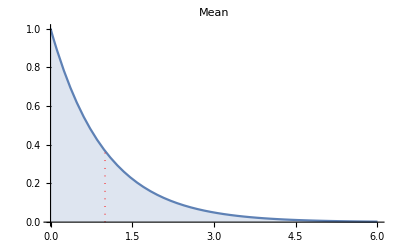
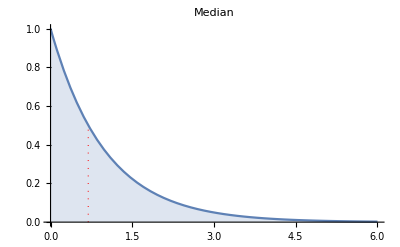
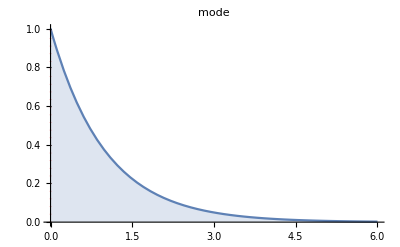

```mathematica
𝒟=ExponentialDistribution[1];
mode[D_]:=x/.Last[NMaximize[PDF[𝒟,x],x]]
Table[With[{m=f[𝒟]},Plot[PDF[𝒟,x],{x,0,6},PlotLabel->ToString[f],Filling->Axis,Epilog->{Directive[Red,Dotted,Thick],Line[{{m,0},{m,PDF[𝒟,m]}}]}]],{f,{Mean,Median,mode}}]
```

### Exponential Distribution

Purpose: time until first arrival?

Parameter and properties:

β>0 is the rate of arrival.

Mean | Variance | PDF | CDF | MGF
1/β | 1/β^2 | Piecewise[{{β e^(-β x), x≥0}, {0, otherwise}}] | Piecewise[{{1-e^(-β x), x≥0}, {0, otherwise}}] | β/(β-t)

The exponential distribution is memoryless, P[X>x+s|X>x]=P[X>s].

```mathematica
Manipulate[
Plot[PDF[ExponentialDistribution[β],x],{x,-1,5},
PlotRange->{0,5},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Exponential Distribution with β="<>ToString[β]
],{β,0.001,5},
Paneled->False]
```

Example:

##### Raindrops keep falling on my head at an average rate of 20 drops/min. What is the probability of having no raindrop falling on my head in a given 3 seconds time interval?

We can use β=1 (drop/3 seconds). The probability of no drop (success) in the first 3 seconds is

P[X>1]=1-∫_0^1 e^-x ⅆx=1-(1-1/e)=1/e=36.7%

Setting other values of β, such as β=20 (drops/min) and calculating P[X>1/20], will give the same result.

##### Given that no raindrop has fallen on my head in the past minute, what is the probability of having no raindrop on my head in another 3 seconds?

Still 36.7% due to the memoryless property.

### Gamma Distribution

Purpose: time until α^th arrival?

Parameter and properties:

α>0 is the number of arrivals you want.

β>0 is the rate of arrival.

Mean | Variance | PDF | MGF
α/β | α/β^2 | Piecewise[{{β^α/α x^(α-1) e^-βx, x>0}, {0, otherwise}}]     where Γ(α)=∫_0^∞ z^(α-1)e^-z ⅆz | (1-t/β)^-α

```mathematica
Manipulate[
Plot[PDF[GammaDistribution[α,1/β],x],{x,-1,5},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Gamma Distribution with α="<>ToString[α]<>", β="<>ToString[β]
],{α,0.001,5},{β,0.001,5},
Paneled->False]
```

### Chi-squared Distribution

Purpose: how is the sum of squares of γ independent standard normal random variables distributed?

Parameter and properties:

γ∈ℕ^+ is the degrees of freedom.

Mean | Variance | PDF | MGF
γ | γ^2 | Piecewise[{{1/(γ/2 2^(γ/2)) x^(γ/2-1)e^(-x/2), x>0}, {0, True}}] | (1-2 t)^(-γ/2)

```mathematica
Manipulate[
Plot[PDF[ChiSquareDistribution[Floor[γ]],x],{x,-1,10},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Chi-squared Distribution with γ="<>ToString[Floor[γ]]
],{γ,1,10},
Paneled->False]
```

### Transformation of Random Variable

X is a continuous RV and φ:ℝ→ℝ is a strictly monotonic and differentiable function, then the PDF of Y=φ∘X is

f_Y(y)=Piecewise[{{f_X(φ^-1(y))·|(d φ^-1(y))/(d y)|, for y∈ran φ}, {0, otherwise}}]

### Normal Distribution

Purpose: not sure which distribution? Then normal distribution!

A Useful Conclusion: ∫_(-∞)^∞ e^(-x^2/c)ⅆx=√(c π), where c>0 is a constant.

Parameter and properties:

μ∈ℝ is the mean,

σ^2>0 is the variance

Mean | Variance | PDF | CDF | MGF
μ | σ^2 | 1/(√(2 π) σ)e^(-1/2((x-μ)/σ)^2) | 1/2 erfc((μ-x)/(√2 σ))       where  erfc(z):=1-2/(√π)∫_0^z e^(-t^2)ⅆt | e^((σ^2 t^2)/2+μ t)

Let X be normally distributed, then Z:=(X-μ)/σ has standard normal distribution (normal distribution with μ=0,σ=1).

```mathematica
Manipulate[
Plot[{PDF[NormalDistribution[μ,σ],x],CDF[NormalDistribution[μ,σ],x]},{x,-5,5},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x"},
PlotLegends->{"PDF","CDF"},
PlotLabel->"Normal Distribution with μ="<>ToString[μ]<>", σ^2="<>ToString[σ^2]
],{μ,-5,5},{σ,0.01,10},
Paneled->False]
```

The standard normal distribution will enable you to find the value of CDF, Φ(x), simply by looking up the following table. There are many forms of standard normal table, and you can check them out here: https://en.wikipedia.org/wiki/Standard_normal_table. With the information we can calculate the following:

P[X≤a]=P[X<a]=Φ(a)

P[a≤X≤b]=P[X≤b]-P[X≤a]=Φ(b)-Φ(a)

```mathematica
TableForm[Table[CDF[NormalDistribution[],x+y],{y,Table[i,{i,0,35}]*0.1},{x,Table[i,{i,0,9}]*0.01}],TableHeadings->{Table[i,{i,0,40}]*0.1,Table[i,{i,0,9}]*0.01}]//Style[#,PrintPrecision->4,FontFamily->"Latin Modern Sans",FontSize->12]&
```

| 0. | 0.01 | 0.02 | 0.03 | 0.04 | 0.05 | 0.06 | 0.07 | 0.08 | 0.09
0. | 0.5 | 0.503989 | 0.507978 | 0.511966 | 0.515953 | 0.519939 | 0.523922 | 0.527903 | 0.531881 | 0.535856
0.1 | 0.539828 | 0.543795 | 0.547758 | 0.551717 | 0.55567 | 0.559618 | 0.563559 | 0.567495 | 0.571424 | 0.575345
0.2 | 0.57926 | 0.583166 | 0.587064 | 0.590954 | 0.594835 | 0.598706 | 0.602568 | 0.60642 | 0.610261 | 0.614092
0.3 | 0.617911 | 0.62172 | 0.625516 | 0.6293 | 0.633072 | 0.636831 | 0.640576 | 0.644309 | 0.648027 | 0.651732
0.4 | 0.655422 | 0.659097 | 0.662757 | 0.666402 | 0.670031 | 0.673645 | 0.677242 | 0.680822 | 0.684386 | 0.687933
0.5 | 0.691462 | 0.694974 | 0.698468 | 0.701944 | 0.705401 | 0.70884 | 0.71226 | 0.715661 | 0.719043 | 0.722405
0.6 | 0.725747 | 0.729069 | 0.732371 | 0.735653 | 0.738914 | 0.742154 | 0.745373 | 0.748571 | 0.751748 | 0.754903
0.7 | 0.758036 | 0.761148 | 0.764238 | 0.767305 | 0.77035 | 0.773373 | 0.776373 | 0.77935 | 0.782305 | 0.785236
0.8 | 0.788145 | 0.79103 | 0.793892 | 0.796731 | 0.799546 | 0.802337 | 0.805105 | 0.80785 | 0.81057 | 0.813267
0.9 | 0.81594 | 0.818589 | 0.821214 | 0.823814 | 0.826391 | 0.828944 | 0.831472 | 0.833977 | 0.836457 | 0.838913
1. | 0.841345 | 0.843752 | 0.846136 | 0.848495 | 0.85083 | 0.853141 | 0.855428 | 0.85769 | 0.859929 | 0.862143
1.1 | 0.864334 | 0.8665 | 0.868643 | 0.870762 | 0.872857 | 0.874928 | 0.876976 | 0.879 | 0.881 | 0.882977
1.2 | 0.88493 | 0.886861 | 0.888768 | 0.890651 | 0.892512 | 0.89435 | 0.896165 | 0.897958 | 0.899727 | 0.901475
1.3 | 0.9032 | 0.904902 | 0.906582 | 0.908241 | 0.909877 | 0.911492 | 0.913085 | 0.914657 | 0.916207 | 0.917736
1.4 | 0.919243 | 0.92073 | 0.922196 | 0.923641 | 0.925066 | 0.926471 | 0.927855 | 0.929219 | 0.930563 | 0.931888
1.5 | 0.933193 | 0.934478 | 0.935745 | 0.936992 | 0.93822 | 0.939429 | 0.94062 | 0.941792 | 0.942947 | 0.944083
1.6 | 0.945201 | 0.946301 | 0.947384 | 0.948449 | 0.949497 | 0.950529 | 0.951543 | 0.95254 | 0.953521 | 0.954486
1.7 | 0.955435 | 0.956367 | 0.957284 | 0.958185 | 0.95907 | 0.959941 | 0.960796 | 0.961636 | 0.962462 | 0.963273
1.8 | 0.96407 | 0.964852 | 0.96562 | 0.966375 | 0.967116 | 0.967843 | 0.968557 | 0.969258 | 0.969946 | 0.970621
1.9 | 0.971283 | 0.971933 | 0.972571 | 0.973197 | 0.97381 | 0.974412 | 0.975002 | 0.975581 | 0.976148 | 0.976705
2. | 0.97725 | 0.977784 | 0.978308 | 0.978822 | 0.979325 | 0.979818 | 0.980301 | 0.980774 | 0.981237 | 0.981691
2.1 | 0.982136 | 0.982571 | 0.982997 | 0.983414 | 0.983823 | 0.984222 | 0.984614 | 0.984997 | 0.985371 | 0.985738
2.2 | 0.986097 | 0.986447 | 0.986791 | 0.987126 | 0.987455 | 0.987776 | 0.988089 | 0.988396 | 0.988696 | 0.988989
2.3 | 0.989276 | 0.989556 | 0.98983 | 0.990097 | 0.990358 | 0.990613 | 0.990863 | 0.991106 | 0.991344 | 0.991576
2.4 | 0.991802 | 0.992024 | 0.99224 | 0.992451 | 0.992656 | 0.992857 | 0.993053 | 0.993244 | 0.993431 | 0.993613
2.5 | 0.99379 | 0.993963 | 0.994132 | 0.994297 | 0.994457 | 0.994614 | 0.994766 | 0.994915 | 0.99506 | 0.995201
2.6 | 0.995339 | 0.995473 | 0.995604 | 0.995731 | 0.995855 | 0.995975 | 0.996093 | 0.996207 | 0.996319 | 0.996427
2.7 | 0.996533 | 0.996636 | 0.996736 | 0.996833 | 0.996928 | 0.99702 | 0.99711 | 0.997197 | 0.997282 | 0.997365
2.8 | 0.997445 | 0.997523 | 0.997599 | 0.997673 | 0.997744 | 0.997814 | 0.997882 | 0.997948 | 0.998012 | 0.998074
2.9 | 0.998134 | 0.998193 | 0.99825 | 0.998305 | 0.998359 | 0.998411 | 0.998462 | 0.998511 | 0.998559 | 0.998605
3. | 0.99865 | 0.998694 | 0.998736 | 0.998777 | 0.998817 | 0.998856 | 0.998893 | 0.99893 | 0.998965 | 0.998999
3.1 | 0.999032 | 0.999065 | 0.999096 | 0.999126 | 0.999155 | 0.999184 | 0.999211 | 0.999238 | 0.999264 | 0.999289
3.2 | 0.999313 | 0.999336 | 0.999359 | 0.999381 | 0.999402 | 0.999423 | 0.999443 | 0.999462 | 0.999481 | 0.999499
3.3 | 0.999517 | 0.999534 | 0.99955 | 0.999566 | 0.999581 | 0.999596 | 0.99961 | 0.999624 | 0.999638 | 0.999651
3.4 | 0.999663 | 0.999675 | 0.999687 | 0.999698 | 0.999709 | 0.99972 | 0.99973 | 0.99974 | 0.999749 | 0.999758
3.5 | 0.999767 | 0.999776 | 0.999784 | 0.999792 | 0.9998 | 0.999807 | 0.999815 | 0.999822 | 0.999828 | 0.999835

Estimation: From the table you can read (how? which number in the table are you using?)

P[-σ<X-μ<σ]=0.68
P[-2σ<X-μ<2σ]=0.95
P[-3σ<X-μ<3σ]=0.997

```mathematica
CDF[NormalDistribution[0,1],1]//N
```

0.841345

Example:

##### A machine in the soft drink factory produces bottles of drinks with mean μ=500 mL and standard deviation σ=1 mL. How many mLs should a bottle have, so that 95% of the bottles produced by this machine have less drink than the bottle?

We need Z=(X-μ)/σ=(X-500)/1>1.65⇒X>501.65.

```mathematica
InverseCDF[NormalDistribution[500,1],0.95]
```

501.645

### Chebyshev Inequality

Purpose: To (roughly) estimate the variance of a random variable.

Mathematical representation: for k∈ℕ\{0}, P[|X|≥c]≤E[|X|^k]/c^k.

Application: P[|X-μ|≥m σ]≤1/m^2.

## Problems in Assignments

### Two Children Paradox - Birthday Party!

What is the probability that the lady’s another child is a girl given that she has a son born in July?

#### Solution

By Cardano’s principle, we can count the number of outcomes in (G,G), (G,B), (B,G), (B,B) respectively. Each grid represent a case such as (an elder girl born in January, a younger boy born in July) and so on.

| An Elder Boy |  |  |  |  |  |  |  |  |  |  | 



A 
Younger
 Boy | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | ■ | ■ | ■ | ■ | ■ | ■ | ■ | ■ | ■ | ■ | ■ | ■
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □
 | □ | □ | □ | □ | □ | □ | ■ | □ | □ | □ | □ | □

(G,G) | (G,B) | (B,G) | (B,B)
Impossible | 12 | 12 | 23

As result, P[another child is girl|boy born in July]=(12+12)/(12+12+23)=24/47. Actually,

P[another child is girl|at least one boy]=2/3≈0.6667
P[another child is girl|at least one boy born in July]=24/47≈0.5106
P[another child is girl|at least one boy born on July 1^st]=(365+365)/(365+365+729)≈0.5003
⋮
P[another child is girl|one elder or younger boy]=1/2=0.5

Conclusion: The probability is highly dependent on our observation and our ability to distinguish two events.

## Problems for Discussion

### Aircraft Maintenance

In order to ensure a high standard of serviceability without incurring unnecessary aircraft delays, an airline such as BEA adopts the following replacement policy for its repairable aircraft components:

An broken component is removed from an aircraft and sent for inspection and repair.

An immediate demand for a serviceable replacement is made to the stores and the replacement is at once fitted to the aircraft.

When the previously broken component has been passed as serviceable, it is placed in the stores.

Suppose we know the following:

Number of demands for a serviceable replacement is on average λ per day.

Number of repair of a broken component is on average μ per day.

Question: how many components should the store prepare?

##### What is the probability of having x demands in t days?

We use the Poisson distribution with parameter λ t (demands/t days). f_(X|t)(x)=P[X=x|T=t]=((e^(-λ t)(λ t))^r)/(x!)=((e^(-λ t)(λ t))^x)/(Γ(x+1)).

##### What is the distribution of time needed to have k components repaired?

We use the Gamma distribution with parameter α=k, β=μ . f_T(t)=μ^k/k t^(k-1) e^(-μ t). k can be interpreted as number of parallel servers that can repair the broken component. 
This time interval is denoted as “lead time”, the time when the shop “takes the lead” as the prepared amount is (hopefully) not used up yet, and the previous batch of repaired components has not yet come.

##### What is the probability of having x demands during the lead time?

The time interval follows a gamma distribution. Using marginal density in joint distribution (quite analogous to the total probability) we can calculate

f_X(x)=∫_0^∞ f_(X|t)(x)f_T(t)ⅆt
=∫_0^∞ ((e^(-λ t)(λ t))^x)/(Γ(x+1))μ^k/k t^(k-1) e^(-μ t)ⅆt
=(μ^k λ^x)/(Γ(x+1)k)∫_0^∞ t^(x+k-1) e^(-(μ+λ)t)ⅆt
=(μ^k λ^x)/((μ+λ)^(x+k)Γ(x+1)k)∫_0^∞ z^(x+k-1) e^-z ⅆz           (z:=(μ+λ)t)
=(Γ(x+k))/(Γ(x+1)k)(μ^k λ^x)/(μ+λ)^(x+k) =(k+x-1
k-1)((λ/μ)/(1+λ/μ))^r(1/(1+λ/μ))^k

So, the probability of having x demands follows a negative binomial distribution with parameters p=(λ/μ)/(1+λ/μ) and r=k. This shows that neg. binomial distribution can be seen as a combination of Poisson and gamma distribution.

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[NegativeBinomialDistribution[k,(λ/μ)/(1+λ/μ)],x],{x,0,20},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","f_X(x)" },
PlotLabel->"Distribution of Number of Demands with λ="<>ToString[λ]<>", μ="<>ToString[μ]<>", k="<>ToString[k]
],{λ,1,5},{μ,1,5},{k,{1,10,100}},Paneled->False]
```

Now, suppose we have n components prepared at the store at any time. The probability of shortage of component will be risk level:=P[having more than n+1 demands]=P[x≥n+1]=∑_(x=n+1)^∞ f_X(x). Different number of k can be used to estimate the risk level of having n components prepared at the store. The rest of the solution will be posted through Piazza.